Practical-2
                                                                                              Newton Raphson Method 

(1) To find a smallest positive root of the function f(x)=x^3-5x+1 perform 5 iterations of the Newton Raphson Method

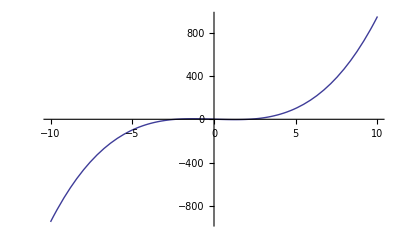

k | xk | f[xk]
0 | 0.5 | -1.375
1 | 0.1764705882 | 0.1231426827
2 | 0.2015680743 | 0.0003492763989
3 | 0.2016396751 | 3.100484314×10^-9
4 | 0.2016396757 | 1.110223025×10^-16
5 | 0.2016396757 | 1.110223025×10^-16

Root after 5 iterations xk = 0.2016396757

Function value at approximated root,f[xk] = 1.110223025×10^-16

```mathematica
NewtonRaphson[x0_,n_,f_]:=Module[{xk1,xk=N[x0]},k=0; Output= {{k,x0,f[x0]}};While[k<n,fPrimexk=f'[xk]; If[fPrimexk==0,Print["The derivative of function at ",k,"th iteration is zero,we can not proceed further with the iterative scheme"];Break[]];xk1=xk-f[xk]/fPrimexk;xk=xk1;k++;Output=Append[Output,{k,xk,f[xk]}];];Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","xk","f[xk]"}}],10]];Print["Root after ",n," iterations xk = ",NumberForm[xk,10]];Print["Function value at approximated root,f[xk] = ",NumberForm[f[xk],10]];];
f[x_] :=x^3-5x+1;
Plot[f[x],{x,-10,10}]
NewtonRaphson[0.5,5,f]
```

(2) Perform 4 iterations of the Newton Raphson Method  to obtain approximate value of  (17)^(1/3) starting with the initial approximation x0=2.

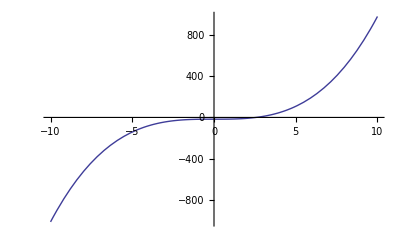

k | xk | f[xk]
0 | 2 | -9
1 | 2.75 | 3.796875
2 | 2.582644628 | 0.2263772599
3 | 2.571331512 | 0.0009901837441
4 | 2.571281592 | 1.922353121×10^-8

Root after 4 iterations xk = 2.571281592

Function value at approximated root,f[xk] = 1.922353121×10^-8

```mathematica
f[x_]= x^3-17;
Plot[f[x],{x,-10,10}]
NewtonRaphson[2,4,f]
```

```mathematica
B=N[17^(1/3),10]
```

2.571281591

(3) Perform 4 iterations of the Newton Raphson Method  to approximate the root of  the function f(x) = x^3+2 x^2-3x-1 near = -3.

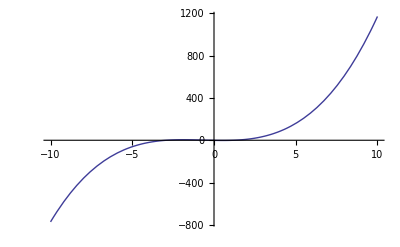

k | xk | f[xk]
0 | -3 | -1
1 | -2.916666667 | -0.04803240741
2 | -2.912241416 | -0.0001320975296
3 | -2.912229179 | -1.008864103×10^-9
4 | -2.912229178 | 0.

Root after 4 iterations xk = -2.912229178

Function value at approximated root,f[xk] = 0.

```mathematica
f[x_]:= x^3+2 x^2-3x-1;
Plot[f[x],{x,-10,10}]
NewtonRaphson[-3,4,f]
```